# Cornell ERL buncher cabity : in.buncher

```mathematica
root=NotebookDirectory[]
```

/Volumes/user/cem52/erl/CERL/lattice_devel/model/in_grid/buncher/

```mathematica
outputCavityFilename = "in.buncher_center_grid.bmad";
outputWallFilename = "in.buncher_center_wall.bmad";
bmadelename = "in.buncher";
frequency = 1.3 10^9(*Hz*);
```

## Options

```mathematica
myplotoptions={BaseStyle->{FontSize->15}, Frame->True};
SetOptions[Plot,myplotoptions];
SetOptions[ListPlot,myplotoptions];
SetOptions[ListLogPlot,myplotoptions];
SetOptions[ListVectorPlot,myplotoptions];
SetOptions[ListDensityPlot,myplotoptions];

cLightN = 299792458.;
μ0N = 4. π 10^-7;
```

```mathematica
FLIP=False;

If[FLIP,
outputCavityFilename = "cavity2_reverse_grid.bmad";
outputWallFilename = "cavity2_reverse_wall.bmad";
bmadelename = "cavity2_reverse";
]
```

## Import

```mathematica
griddatrawfilename="BuncherField20070810_all.txt";
```

```mathematica
griddatrawheader= Import[root<>griddatrawfilename, "Table"][[1;;6]];
griddatraw= Import[root<>griddatrawfilename, "Table"][[2;;]];
```

```mathematica
griddatrawheader//Grid
```

R(cm) | Z(cm) | Er(MV/m) | Ez(MV/m) | Hfi(A/m)
0. | -10. | 0. | 0. | 0.
0. | -9.9 | 0. | 0.0001196 | 0.
0. | -9.8 | 0. | 0.0002423 | 0.
0. | -9.7 | 0. | 0.0003682 | 0.
0. | -9.6 | 0. | 0.0005012 | 0.

```mathematica
griddat= {1/100*#[[1]], 1/100* #[[2]],10^6* #[[3]], 10^6*#[[4]], μ0N *#[[5]]}&/@griddatraw;
xC=1;
zC=2;
ExC=3;
EzC=4;
ByC=5;

If[FLIP,
flip=Table[1, {5}];
flip⟦zC⟧ = -1;
flip⟦EzC⟧ = -1;
flip⟦ByC⟧ = -1;
griddat=griddat.DiagonalMatrix[flip];
]
```

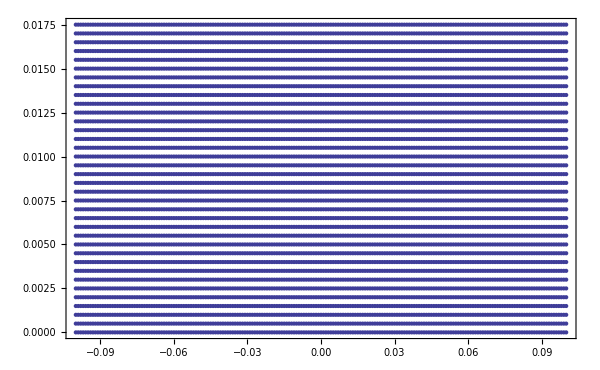

```mathematica
ListPlot[{#[[zC]], #[[xC]]}&/@griddat, ImageSize->600]
```

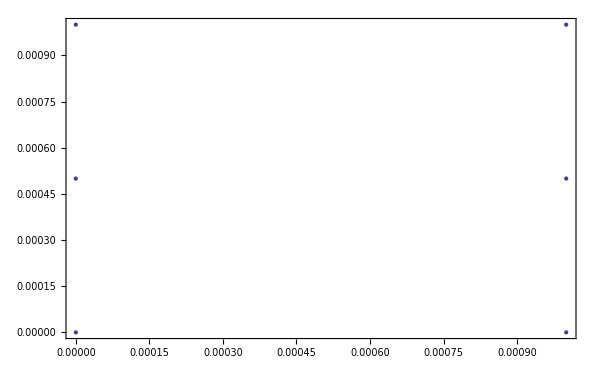

```mathematica
ListPlot[{#[[zC]], #[[xC]]}&/@Select[griddat, (-.001<#[[zC]]<0.0011)&&(-.001<#[[xC]]<0.0011)&], ImageSize->600]
```

## Verify Grid

```mathematica
refdat=griddat;
```

```mathematica
Δz = 0.001;
Δx = 0.0005;

nzpad=2;
nxpad=2;
```

```mathematica
xlist=Sort[#[[xC]]&/@refdat, #1<#2&];xlist=Intersection[xlist,xlist];tmpxmax=Max[xlist];xlist=Join[xlist, Table[tmpxmax+n Δx, {n,1,nxpad}]];
zlist=Sort[#[[zC]]&/@refdat, #1<#2&];zlist=Intersection[zlist,zlist];tmpzmax=Max[zlist];zlist=Join[zlist, Table[tmpzmax+n Δz, {n,1,nzpad}]];
xmax = Max[xlist];xmin = Min[xlist];xsize=xmax-xmin;
zmax = Max[zlist];zmin = Min[zlist];zsize=zmax-zmin;
```

```mathematica
Grid[{{,"min (m)","max (m)", "n_pts"},{"x: ",xmin,xmax, Length[xlist]}, {"z: ",zmin,zmax, Length[zlist]}}, Frame->True, Alignment->Left]
```

| min (m) | max (m) | n_pts
x:  | 0. | 0.0185 | 38
z:  | -0.1 | 0.102 | 203

```mathematica
izof[z_]:=Round[(z -zmin)/Δz];
ixof[x_]:=Round[(x -xmin)/Δx];
zof[iz_]:=zmin + iz Δz;
xof[ix_]:=xmin + ix Δx;
```

```mathematica
ExGrid={izof[#[[zC]]],ixof[#[[xC]]], #⟦ExC⟧}&/@refdat;
```

```mathematica
izof[zmax]
```

202

```mathematica
ixof[xmax]
```

37

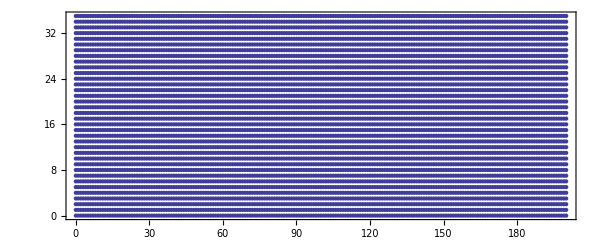

```mathematica
ListPlot[{izof[#[[zC]]],ixof[#[[xC]]]}&/@refdat, ImageSize->600, AspectRatio->Automatic]
```

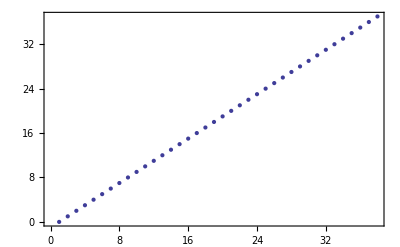

```mathematica
ListPlot[ixof/@xlist]
```

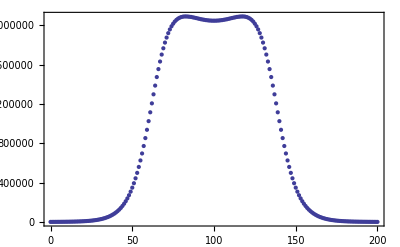

```mathematica
ListPlot[{izof[#⟦zC⟧] ,#[[EzC]]}&/@Select[refdat, #⟦xC⟧==0&]]
```

```mathematica
ListPointPlot3D[{
{ixof[#⟦xC⟧],izof[#⟦zC⟧] ,#[[EzC]]}&/@refdat,
 {ixof[#⟦xC⟧],izof[#⟦zC⟧] ,#[[ExC]]}&/@refdat,
 {ixof[#⟦xC⟧],izof[#⟦zC⟧] ,cLightN#[[ByC]]}&/@refdat}, PlotRange->All, PlotStyle->{{PointSize[Tiny], Blue},{PointSize[Tiny], Red},{PointSize[Tiny], Green}},AxesLabel->{"x index", "z index", "B (T)"}, BaseStyle->{FontSize->15}]
```

-Graphics3D-

## Make Bmad Grid

```mathematica
fieldmapdir =root;
tmpdir="~/Desktop/";
griddatafilename = outputCavityFilename;
wallfilename = outputWallFilename;
```

```mathematica
(*pt format: pt(ir, iz) = ( (ErRe,ErIm), (0,0), (EzRe,EzIm), (0,0), (ErRe,ErIm), (0,0), (BϕRe, BϕIm) , (0,0) ) *)
MakeBmadGrid[dat_]:=Module[{header, body, ptlist},
header = {"{ "};
body = {
{"type = rotationally_symmetric_rz,"},
{"r0 = (",xmin,"," ,0 ,")," },
{"dr = (", Δx,",", Δz, "),"}
};

ptlist ={
"pt(", ixof[ #⟦xC⟧  ], "," ,izof[#⟦zC⟧]  ,") = ( ",
	"(" ,#⟦ExC⟧,", 0 ), 0, ",
			"(", #⟦EzC⟧,", 0 ), ",
	" 0, ( 0, ", #⟦ByC⟧ , "), 0)", ","}&/@dat;
ptlist[[-1,-1]] = "}";
Join[header,body,  ptlist]

]
```

```mathematica
(*Use additional extrapolated data*)
griddata=MakeBmadGrid[refdat ];
```

```mathematica
Export[tmpdir<>griddatafilename ,griddata, "Table", "FieldSeparators"->""];
Run["mv "<>tmpdir<>griddatafilename<>" "<>root<>griddatafilename];
```

## EM Field query

```mathematica
fieldquerydir=root
```

/Volumes/user/cem52/erl/CERL/lattice_devel/model/in_grid/buncher/

```mathematica
tmpdir = "~/Desktop/";
```

```mathematica
it = 1;
ix = 2;
iy =3;
is = 4;
iEx=5;
iEy=6;
iEs=7;
iBx=8;
iBy=9;
iBs=10;
```

### Field on axis

```mathematica
selebeg=0.0;

smin =0+selebeg;
smax = 0.2+selebeg
myt=0;
myx=0.0;
myy=0.0;
sampledat=Table[{myt, myx, myy, s}, {s, smin, smax, (smax-smin)/100}];
Export[root<>"querypoints.dat",Join[{{Length[sampledat]}}, sampledat],  "Table"]
```

0.2

/Volumes/user/cem52/erl/CERL/lattice_devel/model/in_grid/buncher/querypoints.dat

```mathematica
dat=Import[root<>"querypoints.out",  "Table"][[2;;]];
```

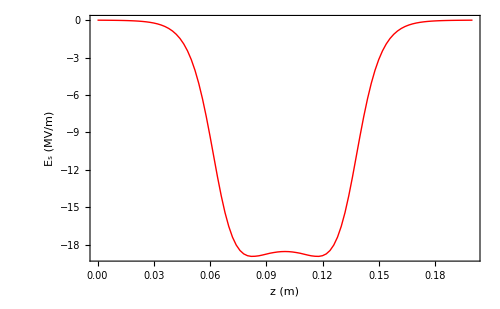

```mathematica
g1=ListPlot[{#[[is]],  10^-3#[[iEs]]}&/@dat, Joined->True,PlotRange->All, Frame->True, BaseStyle->{FontSize->15}, FrameLabel->{"s (m)", "E_x (kV/m)"}, PlotStyle->Red];
Show[g1, PlotRange->All, FrameLabel->{"z (m)", "E_s (MV/m)"}, ImageSize->500]
```

### Field in time

```mathematica
tmin=0;
tmax = 1/frequency;
mys = 0.05;
myx=0.01;
myy=0.0;
sampledat=Table[{t, myx, myy, mys}, {t, tmin, tmax, (tmax-tmin)/100}];
Export[root<>"querypoints.dat",Join[{{Length[sampledat]}}, sampledat],  "Table"]
```

/Volumes/user/cem52/erl/CERL/lattice_devel/model/in_grid/buncher/querypoints.dat

```mathematica
dat=Import[root<>"querypoints.out",  "Table"][[2;;]];
```

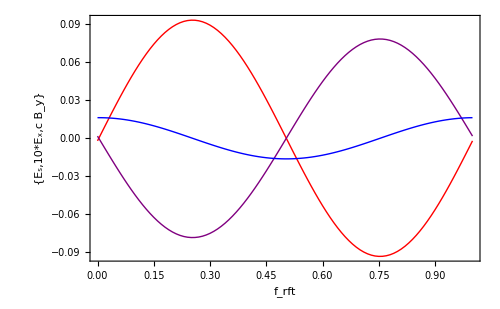

```mathematica
g1=ListPlot[{
{#[[it]]*frequency,  10^-6#[[iEs]]}&/@dat,
{#[[it]]*frequency,  1 10^-6#[[iEx]]}&/@dat,
{#[[it]]*frequency,  10^-6 cLightN#[[iBy]]}&/@dat
}, Joined->True,PlotRange->All, Frame->True, BaseStyle->{FontSize->15}, FrameLabel->{"s (m)", "E_x (MV/m)"}, PlotStyle->{Red,Purple, Blue}];
Show[g1, PlotRange->All, FrameLabel->{"f_rft",{ Style["E_s",Red], Style["10*E_x",Purple], Style["c B_y", Blue]}}, ImageSize->500]
```

### Field on a flat grid

```mathematica
selebeg=0;

smin =0+selebeg;
smax = 0.2+selebeg;
myt=1/8 1/frequency;
myy=0.00;
xmax = 0.017;
nx=50;
ns=200;
xstep=(xmax-xmin)/(nx-1);
 sstep=(smax-smin)/(ns-1);

isof[s_]:=Round[(s-smin)/sstep];
ixof[x_]:=Round[(x -xmin)/xstep];
zof[is_]:=smin + is sstep;
xof[ix_]:=xmin + ix xstep;

sampledat=Flatten[Table[{myt, x, myy, s}, {x,xmin,xmax,xstep},{s, smin, smax,sstep}], 1];Length[sampledat]
```

10000

```mathematica
Export[tmpdir<>"querypoints.dat",Join[{{Length[sampledat]}}, sampledat],  "Table"];
Run["mv "<>tmpdir<>"querypoints.dat"<>" "<>root<>"querypoints.dat"];
```

```mathematica
dat=Import[root<>"querypoints.out",  "Table"][[2;;]];Length[dat]
```

10000

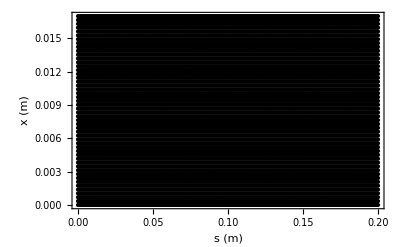

```mathematica
ListPlot[ {#[[is]], #[[ix]]}&/@dat, Frame->True, FrameLabel->{"s (m)", "x (m)"}, BaseStyle->{FontSize->15}, PlotStyle->Black]
```

```mathematica
ListPointPlot3D[{{#⟦is⟧, #⟦ix⟧, #⟦iEs⟧}&/@dat,
 {#⟦is⟧, #⟦ix⟧, #⟦iEx⟧}&/@dat,
 {#⟦is⟧, #⟦ix⟧, cLightN#⟦iBy⟧}&/@dat} , PlotRange->All, PlotStyle->{{PointSize[Tiny], Blue},{PointSize[Tiny], Red},{PointSize[Tiny], Green}}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{{#⟦is⟧, #⟦ix⟧, #⟦iBy⟧}&/@dat} , PlotRange->All, PlotStyle->{{PointSize[Tiny], Blue}}]
```

-Graphics3D-

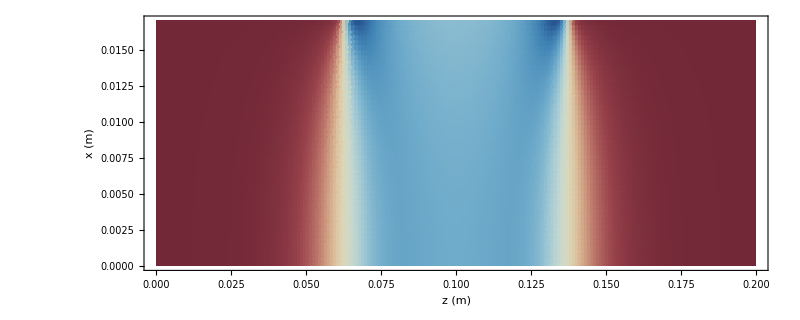

```mathematica
samplegridvalues=Table[0, {ns}, {nx}];
samplegridvalues⟦ isof[#⟦is⟧ ]+1, ixof[ #⟦ix⟧ ] +1⟧ =#⟦iEs⟧;&/@dat;
Show[ListDensityPlot[Transpose[samplegridvalues], DataRange->{{smin,smax}, {xmin,xmax}}, AspectRatio->Automatic, PlotRange->{{smin,smax}, {xmin,xmax}}, ColorFunction->"RedBlueTones", FrameLabel->{"z (m)", "x (m)"}],ImageSize->800]
```

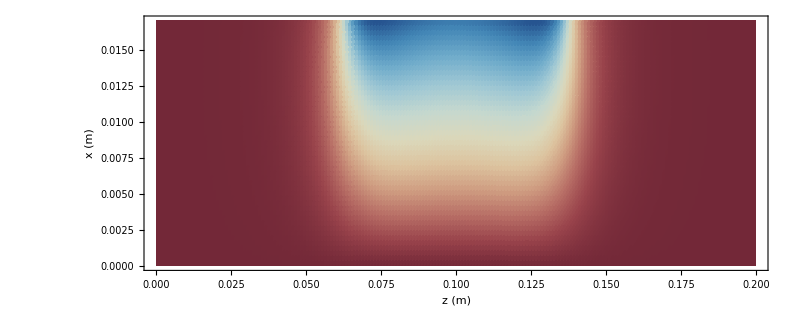

```mathematica
samplegridvalues=Table[0, {ns}, {nx}];
samplegridvalues⟦ isof[#⟦is⟧ ]+1, ixof[ #⟦ix⟧ ] +1⟧ =#⟦iBy⟧;&/@dat;
Show[ListDensityPlot[Transpose[samplegridvalues], DataRange->{{smin,smax}, {xmin,xmax}}, AspectRatio->Automatic, PlotRange->{{smin,smax}, {xmin,xmax},All}, ColorFunction->"RedBlueTones",FrameLabel->{"z (m)", "x (m)"}, PlotRange->All],ImageSize->800]
```

### Field on surface

```mathematica
selebeg=0.0;
myt=0;
myy=0.0;
sampledat=Select[{myt,#⟦xC⟧,myy, #⟦zC⟧-zmin}&/@walldat, 0<#⟦4⟧<0.48&];
Export[root<>"querypoints.dat",Join[{{Length[sampledat]}}, sampledat],  "Table"];
```

```mathematica
dat=Import[root<>"querypoints.out",  "Table"][[2;;]];
```

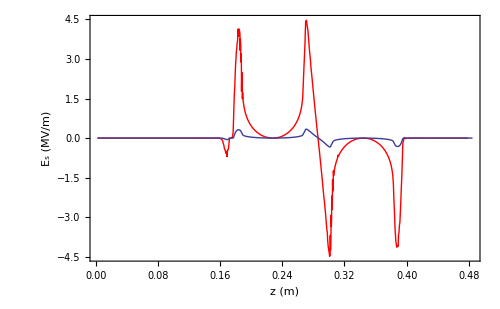

```mathematica
g1=ListPlot[{#[[is]],  10^-6#[[iEs]]}&/@dat, Joined->True,PlotRange->All, Frame->True, BaseStyle->{FontSize->15}, FrameLabel->{"s (m)", "E_x (MV/m)"}, PlotStyle->Red];
g2=ListPlot[{#⟦zC⟧-zmin, 10^-6#⟦EzC⟧}&/@walldat, Joined->True, AxesOrigin->{0,0}, PlotRange->All, FrameLabel->{"z (m)", "Ez (MV/m)"}];
Show[g1,g2, PlotRange->All, FrameLabel->{"z (m)", "E_s (MV/m)"}, ImageSize->500]
```

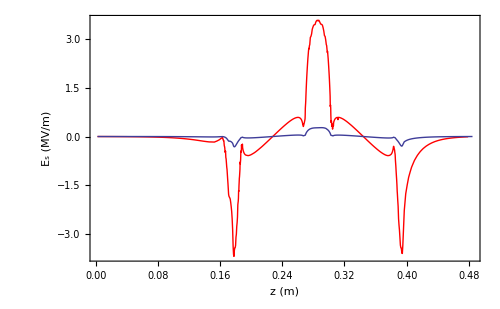

```mathematica
g1=ListPlot[{#[[is]],  10^-6#[[iEx]]}&/@dat, Joined->True,PlotRange->All, Frame->True, BaseStyle->{FontSize->15}, FrameLabel->{"s (m)", "E_x (MV/m)"}, PlotStyle->Red];
g2=ListPlot[{#⟦zC⟧-zmin,  10^-6#⟦ExC⟧}&/@walldat, Joined->True, AxesOrigin->{0,0}, PlotRange->All, FrameLabel->{"z (m)", "Ez (MV/m)"}];
Show[g1,g2, PlotRange->All, FrameLabel->{"z (m)", "E_s (MV/m)"}, ImageSize->500]
```

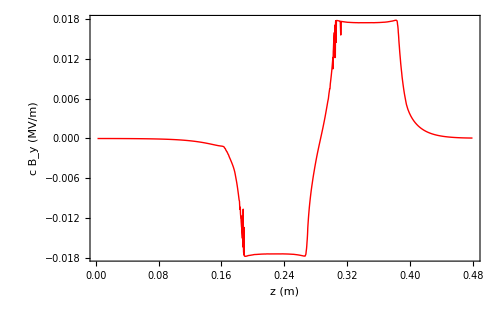

```mathematica
g1=ListPlot[{#[[is]],-#[[iBy]]}&/@dat, Joined->True,PlotRange->All, Frame->True, BaseStyle->{FontSize->15}, FrameLabel->{"s (m)", "E_x (MV/m)"}, PlotStyle->Red];
g2=ListPlot[{#⟦zC⟧-zmin, #⟦ByC⟧}&/@walldat, Joined->True, AxesOrigin->{0,0}, PlotRange->All, FrameLabel->{"z (m)", "Ez (MV/m)"}];
Show[g1,PlotRange->All, FrameLabel->{"z (m)", "c B_y (MV/m)"}, ImageSize->500]
```